# Lecture 31: SVD Algorithms

Time to learn how to compute the SVD A=U.Σ.V^*.  Perhaps not surprisingly, SVD algorithms look quite a bit like eigenvalue algorithms.

## Eigenvalues of A^*.A

If A=U.Σ.V^* is the SVD then A^*.A=(U.Σ.V^*)^*.U.Σ.V^*=V.Σ^*.U^*.U.Σ.V^*=V.Σ^*.Σ.V^* since U is unitary.  More over, since Σ is real we wind up with A^*.A=V.Σ^2.V^*.  We can compute the Hermitian eigenvalue problem A^*.A=V.Λ.V^* then compute 
Σ as the diagonal matrix of the positive square roots of Λ and compute U from U.Σ=A.V.  The problem with this (or similarly computing with A.A^*) is that we know this problem (just like the normal equations) is more sensitive to perturbations than it needs to be.   The fundamental problem is the we formed the product. The stability problem is most extreme for the smaller singular values.

## Eigenvalues of H=(0 | A^* A | 0)

A direct computation shows that if A=U.Σ.V^* then 
	(0 | A^*
A | 0).(V | V
U | -U)=(A^*.U | -A^*.U
A.V | A.V)
Since A=U.Σ.V^* we have A.V=U.Σ.V^*.V=U.Σ.  
Since A^*=V.Σ.U^* we have that A^*.U=V.Σ.U^*.U=V.Σ. 
So
	(0 | A^*
A | 0).(V | V
U | -U)=(V.Σ | -V.Σ
U.Σ | U.Σ)=(V | V
U | -U).(Σ | 0
0 | -Σ).
In words, the eigen values of the big Hermitian matrix in the heading are the ± the singular values. The singular vectors are in the eigenvectors.

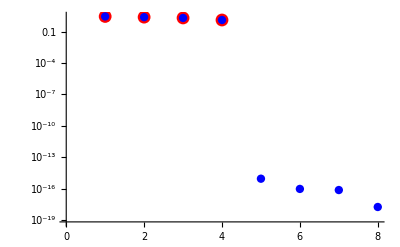

```mathematica
{m,n}={12,4};
A=RandomReal[{-1,1},{m,n}];
H=ArrayFlatten[({{0, ConjugateTranspose[A]}, {A, 0}})];
MatrixPlot[H];
{λ,V}=Eigensystem[H];
σ=SingularValueList[A];
ListLogPlot[{σ,Select[λ,Positive]},GridLines->Automatic,
PlotStyle->{Directive[Red,PointSize[0.023]],Directive[Blue, PointSize[0.015]]}]
```

This stable algorithm is what computes 99.999% of all SVDs in the world.  It is sneaky because it does not actualy need to make the big H matrix! Just like for eigenvalues there is a preliminary reduction.

For singular values, we can get to an upper bi-diagonal matrix! The bi-diagonal form is then iteratively reduced to a diagonal form.  If you only want singular values you do not need to keep the rotations

### Bi-diagonalization

The plan is to use Householder operations on the left and right to rotate the matrix to an upper bi-diagonal form. I am going to call the right rotations U and the left rotations V.

Here is a preliminary script.

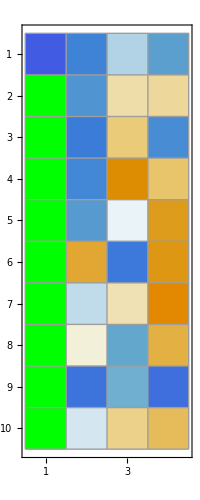

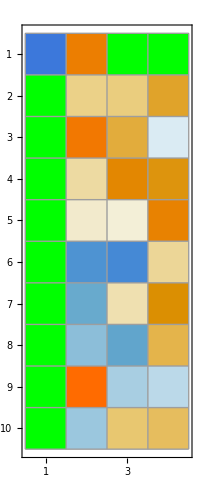

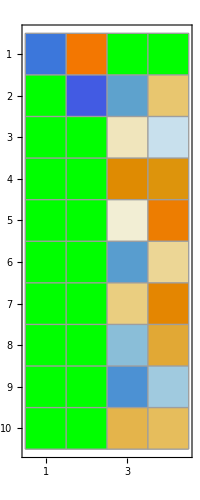

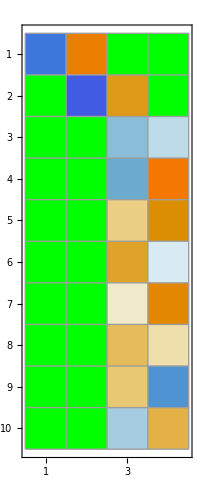

```mathematica
SetOptions[MatrixPlot,ColorRules->{0->Green}, Mesh->All];
{m,n}={10,4};
A=A0=RandomReal[{-1,1},{m,n}];
U=HouseMat[A⟦1;;m,1⟧];
A⟦1;;m,1;;n⟧=Chop[U.A⟦1;;m,1;;n⟧];
MatrixPlot[A]
V=HouseMat[A⟦1,2;;n⟧];
A⟦1;;m,2;;n⟧=Chop[A⟦1;;m,2;;n⟧.V];
MatrixPlot[A]
U=HouseMat[A⟦2;;m,2⟧];
A⟦2;;m,2;;n⟧=Chop[U.A⟦2;;m,2;;n⟧];
MatrixPlot[A]
V=HouseMat[A⟦2,3;;n⟧];
A⟦2;;m,3;;n⟧=Chop[A⟦2;;m,3;;n⟧.V];
MatrixPlot[A]
```

```mathematica
TableForm[Map[SingularValueList,{A,A0}]]
```

2.32707 | 1.76777 | 1.31506 | 0.927963
2.32707 | 1.76777 | 1.31506 | 0.927963

## From Lecture 10: Householder Reflection Code

### Householder Reflections Matrix Functions

If v is a unit vector parallel to 
	sign(a⟦1⟧)||a||e_1+a
then the orthogonal matrix Q=I-2 v⊗v satisfies
	Q.a=||a||e_1
In other words, Q rotates the vector a to align with the vector e_1.

```mathematica
HouseVec[a_]:= Module[{v=a},
v⟦1⟧+=Sign[a⟦1⟧]Norm[a];
v/Norm[v]]
HouseMat[a_]:= Module[{v},
v=HouseVec[a];
IdentityMatrix[Length[a]]-2 KroneckerProduct[v,v]]
```

```mathematica
m=21;
a=RandomReal[{-1,1},m];
Q=HouseMat[a];
Norm[Q.Qᵀ -IdentityMatrix[m]]
Chop[Q.a]
```

4.46272×10^-16

{2.88227,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Householder Reflections Action Functions

There is no need to build the Householder matrix.  All we need to be able to do is apply the matrix to a vector x.

```mathematica
HouseActionVec[x_,a_]:= Module[{v},
v=HouseVec[a];
x-2 v (v.x)]
```

As always TEST!

```mathematica
m=14;
{x,a}=RandomReal[{-1,1},{2,m}];
Q=HouseMat[a];
Map[Norm,{Q.x-HouseActionVec[x,a],Q.a- HouseActionVec[a,a]}]
```

{3.97399×10^-16,1.12638×10^-15}